# TheRealCStover/Trigonometry

A collection of lesser-known circular and hyperbolic trig functions and their inverses

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"Trigonometry.nb"Documentation/English/Guides/Trigonometry.nb

"ReferencePages"

"Symbols"

"Chord.nb"Documentation/English/ReferencePages/Symbols/Chord.nb

"Cohavercosine.nb"Documentation/English/ReferencePages/Symbols/Cohavercosine.nb

"Cohaversine.nb"Documentation/English/ReferencePages/Symbols/Cohaversine.nb

"Covercosine.nb"Documentation/English/ReferencePages/Symbols/Covercosine.nb

"Coversine.nb"Documentation/English/ReferencePages/Symbols/Coversine.nb

"Excosecant.nb"Documentation/English/ReferencePages/Symbols/Excosecant.nb

"Exsecant.nb"Documentation/English/ReferencePages/Symbols/Exsecant.nb

"Hacovercosine.nb"Documentation/English/ReferencePages/Symbols/Hacovercosine.nb

"Hacoversine.nb"Documentation/English/ReferencePages/Symbols/Hacoversine.nb

"Havercosine.nb"Documentation/English/ReferencePages/Symbols/Havercosine.nb

"InverseChord.nb"Documentation/English/ReferencePages/Symbols/InverseChord.nb

"InverseCohavercosine.nb"Documentation/English/ReferencePages/Symbols/InverseCohavercosine.nb

"InverseCohaversine.nb"Documentation/English/ReferencePages/Symbols/InverseCohaversine.nb

"InverseCovercosine.nb"Documentation/English/ReferencePages/Symbols/InverseCovercosine.nb

"InverseCoversine.nb"Documentation/English/ReferencePages/Symbols/InverseCoversine.nb

"InverseExcosecant.nb"Documentation/English/ReferencePages/Symbols/InverseExcosecant.nb

"InverseExsecant.nb"Documentation/English/ReferencePages/Symbols/InverseExsecant.nb

"InverseHacovercosine.nb"Documentation/English/ReferencePages/Symbols/InverseHacovercosine.nb

"InverseHacoversine.nb"Documentation/English/ReferencePages/Symbols/InverseHacoversine.nb

"InverseHavercosine.nb"Documentation/English/ReferencePages/Symbols/InverseHavercosine.nb

"InverseVercosine.nb"Documentation/English/ReferencePages/Symbols/InverseVercosine.nb

"InverseVersine.nb"Documentation/English/ReferencePages/Symbols/InverseVersine.nb

"Vercosine.nb"Documentation/English/ReferencePages/Symbols/Vercosine.nb

"Versine.nb"Documentation/English/ReferencePages/Symbols/Versine.nb

"Tutorials"

"img"

"Diagram1.pdf"img/Diagram1.pdf

"Diagram1.png"img/Diagram1.png

"Diagram1Trans.png"img/Diagram1Trans.png

"Diagram.nb"img/Diagram.nb

"Kernel"

"Trigonometry.wl"Kernel/Trigonometry.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

In a standard trigonometry course, we typically learn about six functions (and their inverses): sin(x), cos(x), tan(x), csc(x), sec(x), and tan(x); this may or may not be extended later to cover the six hyperbolic trig functions (e.g. sinh(x)) and/or their inverses (e.g. sin^-1(x), sinh^-1(x)).

A less-known fact is that trigonometry actually consists of over two dozen other circular and hyperbolic functions, each of which has a well-defined inverse. These mysterious trig functions are closely related to the more well-known relatives that we all know and love today, and though they're rarely used, these functions were ubiquitous a few centuries back, being employed both in academia and in various applications (e.g. map making, ocean exploration, etc.).

Mathematica has a couple of these little-used trig functions built in (namely Haversine and InverseHaversine), but the rest remain unrepresented; this absence is the underlying motivation for Trigonometry. All of the 50+ functions in Trigonometry work naturally with the entire Wolfram Language framework, and their immediate availability allows a better understanding of the relationships and history of both trigonometry and mathematics as a whole. These functions provide both a learning opportunity and a teaching tool, thus contributing to the enrichment of mathematics as a whole.

### Details

Trigonometry consists of a number of "circular" trigonometric functions, as well as their hyperbolic analogues and the inverses of all of them.

Because of how they're defined, the functions in Trigonometry fit perfectly into all the common Wolfram Language functionality including D, Integrate, Series, Plot, etc.

### Main Guide Page

"Documentation/English/Guides/Trigonometry.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Evaluate numerically:

```mathematica
#[0.5]&/@{Versine,Vercosine,Havercosine,Coversine,Covercosine,Hacoversine,Cohaversine,Hacovercosine,Cohavercosine,Exsecant,Excosecant,Chord}
```

{0.122417,1.87758,0.938791,0.520574,1.47943,0.260287,0.260287,0.739713,0.739713,0.139494,1.08583,0.494808}

An argument given in radians:

```mathematica
#[5Pi/3]&/@{Versine,Vercosine,Havercosine,Coversine,Covercosine,Hacoversine,Cohaversine,Hacovercosine,Cohavercosine,Exsecant,Excosecant,Chord}
```

{1/2,3/2,3/4,1+(√3)/2,1-(√3)/2,1/2 (1+(√3)/2),1/2 (1+(√3)/2),1/2 (1-(√3)/2),1/2 (1-(√3)/2),1,-1-2/(√3),1}

Use Degree to specify an argument in degrees:

```mathematica
#[60 Degree]&/@{Versine,Vercosine,Havercosine,Coversine,Covercosine,Hacoversine,Cohaversine,Hacovercosine,Cohavercosine,Exsecant,Excosecant,Chord}
```

{1/2,3/2,3/4,1-(√3)/2,1+(√3)/2,1/2 (1-(√3)/2),1/2 (1-(√3)/2),1/2 (1+(√3)/2),1/2 (1+(√3)/2),1,-1+2/(√3),1}

Plot over a subset of the reals:

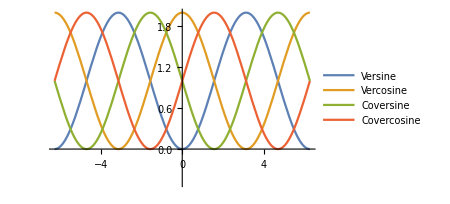
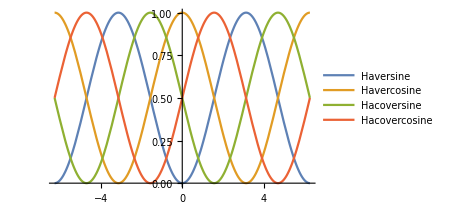
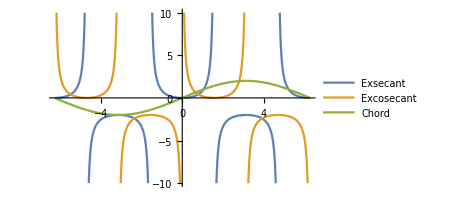

```mathematica
{
With[{list1={Versine,Vercosine,Coversine,Covercosine}},Plot[Evaluate[#[x]&/@list1],{x,-2Pi,2Pi},PlotRange->{Automatic,{-0.5,2}},PlotLegends->list1,ImageSize->333]],
With[{list2={Haversine,Havercosine,Hacoversine,Hacovercosine}},Plot[Evaluate[#[x]&/@list2],{x,-2Pi,2Pi},PlotRange->{0,1},PlotLegends->list2,ImageSize->333]],
With[{list3={Exsecant,Excosecant,Chord}},Plot[Evaluate[#[x]&/@list3],{x,-2Pi,2Pi},PlotRange->{-10,10},PlotLegends->list3,ImageSize->333]]
}
```

### Scope

## Source & Additional Information

### Creator

Christopher Stover

### Source Control Repository

https://github.com/stoverc/Trigonometry

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

DisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more informationLocal files

DisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more informationWolfram account

DisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more informationExternal services

DisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies <+$Path+>, <+Directory+>, or similar
◼ Installs additional paclets or dependencies
◼ Creates, modifies or deletes symbols outside of the Publisher`PacletBaseName` context
◼ Creates or imports non-public <+ResourceObject+> content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more informationWL system configuration

DisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of <+SystemCredential+>Click for more informationOS configuration

DisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via <+ExternalEvaluate+>
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more informationLocal system interactions

DisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more informationOther

## Author Notes

Additional information about limitations, issues, etc.